# Components for Pneumatic Systems

```mathematica
<<C:\\Hopsan\Compgen\CompgenNG02.mx
```

```mathematica
Off[General::"spell1"]
```

p1 = pgas[n1];	 qm1 = qmgas[n1];	 cp1 = cgas[n1];	 ZcEP1 = Zcgas[n1];
p2 = pgas[n2];	 qm2 = qmgas[n2];	 cp2 = cgas[n2]; 	 ZcEP2 = Zcgas[n2];
T1 = Tgas[n1];	 dE1 = dEgas[n1];
T2 = Tgas[n2];	 dE2 = dEgas[n2];

## Volume 2

```mathematica
domain="Pneumatic";
displayName="Volume2";
brief="Pneumatic volume";
componentType="ComponentC";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFile[domain,displayName];
ResetComponentVariables[];
```

```mathematica
outputVariables  = {{mgas,0.001,double,"kg","Mass in volume"}};
```

```mathematica
inputParameters = {
{V,0.001,double,"m3","Volume"},
{R,287.,double,"J/Kg K","Gas constant"},
{cv,718.,double,"J/Kg K","heatcoeff"},
{ka,0.,double,"J/Ks","heat conductance"},
{T0,300.,double,"K","Outside temperature"},
{alpha,0.1,double,"","numerical damping"},
{pmin,1.,double,"Pa","min pressure (very low)"}
		};
```

```mathematica
portConnections={
	PneumaticCport[gas1,0.,"fluid port 1",{0,0.5,270}],
	PneumaticCport[gas2,0.,"fluid port 2",{0,0.5,90}]};
```

```mathematica
nodeConnections={
	PneumaticCport[gas1,0.,"fluid port 1",{0,0.5,270}],
	PneumaticCport[gas2,0.,"fluid port 2",{0,0.5,90}]};
```

### Pressure and temperature

#### Definition of rules

```mathematica
Unprotect[D];
D[x_  y_,t_]:=D[x,t]y+x D[ y,t];
D[x_ /y_,t_]:=D[x,t]/y-x D[ y,t]/y^2;
D[x_+y_,t_]:=D[x,t]+D[y,t];
```

```mathematica
p=.;
dotv =.;
U=.;
H=.;
dotU=.;
T=.;
dotv=.;
Tav=.;
```

```mathematica
D[m, t]= qm  ;
D[p, t] = dotp;
D[v, t] = dotv;
D[T, t] = dotT;
D[U, t]= dotU;
D[H, t]= dotH;
```

### Equations

```mathematica
eqp = p == (mgas R T)/V;
```

```mathematica
eqU = U == mgas cv T;
```

```mathematica
eqH = H == U +  p V;
```

H=m T(c_v + R)

```mathematica
T
```

T

```mathematica
eqT = T== (U +  p V)/(mgas(cv + R))
```

T==(U+p V)/(mgas (cv+R))

```mathematica
eqdotp =D[eqp[[1]],t]==D[eqp[[2]],t]
```

dotp==(dotT mgas R)/V

```mathematica
eqdotS = dotU == dotSq T + dotSew T
```

dotU==dotSew T+dotSq T

```mathematica
dotUq =   qm cv Tin;
DotUew = p qv;
```

```mathematica
eqdotU = dotE == dotUq + dotUew
```

dotE==dotUew+cv qm Tin

```mathematica
dotU
```

dotU

```mathematica
dotU =dotE-D[p V,t]
```

dotE-dotp V

```mathematica
qv = qm R Tin/p
```

(qm R Tin)/p

```mathematica
eqH[[2]]
```

U+p V

```mathematica
eqdotT = dotT ==D[eqH[[2]]/(mgas (cv+R)),t]
```

dotT==dotE/(mgas (cv+R))

### Solving the quations

```mathematica
dotV=.;
```

The system of equations

```mathematica
{eqdotp,eqp,eqU}
```

{dotp==(dotT mgas R)/V,p==(mgas R T)/V,U==cv mgas T}

Solving for dotp,dotT,m, and U

```mathematica
{eqdotp,eqp,eqdotS}
```

{dotp==(dotT mgas R)/V,p==(mgas R T)/V,dotE-dotp V==dotSew T+dotSq T}

```mathematica
eqs = Simplify[Solve[{eqdotp,eqdotT,eqp,eqU},{dotp,dotT,mgas,U}]]
```

{{dotp→(dotE R)/((cv+R) V),dotT→(dotE R T)/(cv p V+p R V),mgas→(p V)/(R T),U→(cv p V)/R}}

```mathematica
dp = Collect[dotp/.eqs[[1]],{qm,dotv}]
```

(dotE R)/((cv+R) V)

```mathematica
dT=  Collect[dotT/.eqs[[1]],{qm,dotv}]
```

(dotE R T)/(cv p V+p R V)

For the case of constant volume

```mathematica
dotv = 0;
```

```mathematica
dotp
```

dotp

```mathematica
eqs = Solve[{eqdotp,eqdotT,eqU,eqp},{dotp,dotT,mgas,U}]
```

{{dotp→(dotE R)/((cv+R) V),dotT→(dotE R T)/(p (cv+R) V),mgas→(p V)/(R T),U→(cv p V)/R}}

```mathematica
dp = Collect[dotp/.eqs[[1]],{qm,dotS}]
```

(dotE R)/((cv+R) V)

The pressure is a function of the entropy flow dotS only. The massflow enters only inderectly since it affects T.

The energy-pressure capacitance is defined as

```mathematica
Cep = dotE/dp
```

((cv+R) V)/R

When solving the equation, temperature and mass  are reduced to "book-keeping variables" that can be calculated after the pressure has been calculated.

The mass can be calculated from

```mathematica
mexpr0=.
```

```mathematica
systemEquationsDa= {mgas - (qm1+qm2)/s};
```

```mathematica
systemVariables={mgas};
```

```mathematica
boundaryEquations=.;
```

```mathematica
T = Tav;
p = pav;
```

The temperature can be calculated as

```mathematica
Texpr = T/.Solve[eqp,T][[1]]
```

(pav V)/(mgas R)

This is to be preffered from a numerical point of view

fak=1/(1-alfa)

1/(1-alfa)

```mathematica
ZcdEpexpr = (fak mTimestep)/Cep
```

(fak mTimestep R)/((cv+R) V)

```mathematica
h
```

h

```mathematica
Cep
```

((cv+R) V)/R

### Characteristics

```mathematica
c = {cp1,cp2}
```

{cp1,cp2}

```mathematica
q = {qm1,qm2,dE1,dE2}
```

{qm1,qm2,dE1,dE2}

```mathematica
dE = {dE1,dE2}
```

{dE1,dE2}

```mathematica
ZcdEp=.
```

```mathematica
zc={{ZcdEp,0},
		{0,ZcdEp}}
```

{{ZcdEp,0},{0,ZcdEp}}

```mathematica
cd={cdp1expr,cdp2expr}
```

{cdp1expr,cdp2expr}

```mathematica
dEk ={ka/2 (T0-Tav),ka/2 (T0-Tav)}
```

{1/2 ka (T0-Tav),1/2 ka (T0-Tav)}

```mathematica
{cdp2expr,cdp1expr} = c+2 zc.(dE+dEk)
```

{cp1+2 (dE1+1/2 ka (T0-Tav)) ZcdEp,cp2+2 (dE2+1/2 ka (T0-Tav)) ZcdEp}

#### Filtering of characteristics

```mathematica
cp1expr=alpha cp1rf +(1-alpha) cpl1r;
cp2expr=alpha cp2rf +(1-alpha) cpl2r;
```

```mathematica
cp1expr = cdp1+Zc1 ka/2 (T0-Tav);
cp2expr = cdp2+Zc2 ka/2(T0-Tav);
```

```mathematica
fak=.
```

initialExpressions = {{fak, 1/(1 - alpha), double, "", "Correction factor"}}

```mathematica
initialExpressions= {
{Tav ,(T1+T2)/2},
{pav ,(p1+p2)/2 },
{Zcgas1,ZcdEpexpr},
{Zcgas2,ZcdEpexpr},
{cp1, pgas1},
{cp2, pgas2}};
```

```mathematica
localExpressions ={
{fak,1/(1-alpha),double,"","Correction factor"},
{pav ,onPositive [p1+p2-pmin](p1+p2-pmin)/2 +pmin/2,double,"",""},
{Tav ,Texpr,double,"",""},
{ZcdEp,ZcdEpexpr,double,"",""},
{cdp1,cdp1expr,double,"",""},
{cdp2,cdp2expr,double,"",""}
};
```

```mathematica
expressions={
{Tgas1,Tav},
{Tgas2,Tav},
{cp1,cp1expr},
{cp2,cp2expr},
{Zcgas1,ZcdEp},
{Zcgas2,ZcdEp}
};
```

```mathematica
localExpressions
```

{{fak,1/(1-alpha),double,,Correction factor},{pav,pmin/2+1/2 (p1+p2-pmin) onPositive[p1+p2-pmin],double,,},{Tav,(pav V)/(mgas R),double,,},{ZcdEp,(fak mTimestep R)/((cv+R) V),double,,},{cdp1,cp2+2 (dE2+1/2 ka (T0-Tav)) ZcdEp,double,,},{cdp2,cp1+2 (dE1+1/2 ka (T0-Tav)) ZcdEp,double,,}}

```mathematica
expressions
```

{{Tgas1,Tav},{Tgas2,Tav},{cp1,cdp1+1/2 ka (T0-Tav) Zc1},{cp2,cdp2+1/2 ka (T0-Tav) Zc2},{Zcgas1,ZcdEp},{Zcgas2,ZcdEp}}

```mathematica
Compgen[file]
```

Part::partd: Part specification delayedPart ⟦ 1, 1 ⟧ is longer than depth of object.

XMLElement::cntsList: XMLElement["modelobject", {« 1 », « 1 »}, {XMLElement["icon", {"isopath" → "PneumaticVolume2.svg", "iconrotation" → "ON", "userpath" → "PneumaticVolume2.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.333333, "a" → "90", "name" → "Pgas1"}, {}], XMLElement["portpose", {« 1 »}, {}], XMLElement["portpose", {"x" → "0.5", "y" → "1", "a" → "90", "name" → "Pmgas"}, {}]}]}] in XMLElement["hopsanobjectappearance", {"version" → "0.1"}, XMLElement["modelobject", {"typename" → "PneumaticVolume2", "displayname" → "PneumaticVolume2"}, {XMLElement["icon", {"isopath" → "PneumaticVolume2.svg", "iconrotation" → "ON", "userpath" → "PneumaticVolume2.svg"}, {}], « 1 »}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "y" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.666667 in "y" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

PneumaticVolume2.xml

## Orifice

```mathematica
domain="Pneumatic";
displayName="Orifice";
brief="Pneumatic orifice";
componentType="ComponentQ";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFile[domain,displayName];
ResetComponentVariables[];
```

```mathematica
inputParameters = {
		{Cd,0.65,double,"","Discharge coefficient"},
		{R,287.,double,"J/Kg K","Gas constant"},
		{cv,718,double,"J/Kg K","heatcoeff"},
		{eps,0.02,double,"","Linearisation coeff"}};
```

```mathematica
inputVariables = {{A0,1.*10^-6,double,"m2","Area"}};
```

```mathematica
portConnections = {
			PneumaticQport[1,100000.,"fluid port 1",{0,0.5,270}],
			PneumaticQport[2,100000.,"fluid port 2",{1,0.5,90}]};
```

```mathematica
nodeConnections={
	PneumaticCport[1,100000.,"fluid port 1"],
	PneumaticCport[2,100000.,"fluid port 2"]};
```

### The system of equations

The flow at inlet and outlet are equal but with oposit sign.

```mathematica
qmp1e = -qmp2
```

-qmp2

```mathematica
Ng1=1
```

1

```mathematica
qma:=(p10 Cd A0 Kg Ng)/(√T1)
```

```mathematica
qmb:=(p20 Cd A0 Kg Ng)/(√T2)
```

```mathematica
Nga2:=keps (SqrabsL[((pp2/pp1)^(2/kappa)-(pp2/pp1)^((kappa+1)/kappa))/Ndenom,eps])
```

```mathematica
Ngb2:=keps(SqrabsL[((pp1/pp2)^(2/kappa)-(pp1/pp2)^((kappa+1)/kappa))/Ndenom,eps])
```

```mathematica
Ng:= onPositive[p10-p20](onPositive[pp2/pp1-crit]Nga2 + onNegative[pp2/pp1-crit]Ng1 )
	+ onNegative[p10-p20](onPositive[pp1/pp2-crit]Ngb2 + onNegative[pp1/pp2-crit]Ng1 );
```

```mathematica
dEp1q =(onPositive[qmp1e] qmp1e cv T2+onNegative[qmp1e]qmp1e  T1 cv);
dEp1ew = (onPositive[qmp1e] qmp1e R T2+onNegative[qmp1e]qmp1e T1  R);
dEp1gh=R onPositive[qmp1e] qmp1e T2 (1-pp1/pp2);
```

```mathematica
dEp2q =(onPositive[qmp2] qmp2 cv T1+onNegative[qmp2]qmp2  T2 cv);
dEp2ew = (onPositive[qmp2] qmp2 R T1+onNegative[qmp2]qmp2 T2  R);
dEp2gh=R onPositive[qmp2] qmp2 T1 (1-pp2/pp1);
```

```mathematica
systemEquationsDa={qmp2-( onPositive[p10-p20] qma - onNegative[p10-p20] qmb),
		dEp1-Simplify[dEp1q+dEp1ew+dEp1gh],
		dEp2-(dEp2q+dEp2ew+dEp2gh)
			};
```

```mathematica
systemEquationsDa={qmp2-( onPositive[p10-p20] qma - onNegative[p10-p20] qmb),
		dEp1-(onPositive[qmp1e] qmp1e cp T2+onNegative[qmp1e]qmp1e cp T1+R onPositive[qmp1e] qmp1e T2 (1-pp1/pp2)),
		dEp2-(onPositive[qmp2] qmp2 cp T1+onNegative[qmp2]qmp2 cp T2+R onPositive[qmp2] qmp2 T1 (1-pp2/pp1))		
	};
```

```mathematica
systemVariables = {qmp2,dEp1,dEp2,pp1,pp2};
```

### Plotting flow as a function of pressure

#### Parameters

```mathematica
Fa1[qmp2_,pp1_,pp2_]:=qmp2-( onPositive[pp1-pp2] qma - onNegative[pp1-pp2] qmb)
```

```mathematica
keps=1/(-√eps+√(1+eps));
		Kg=√(kappa/R(2/(kappa+1))^((kappa+1)/(kappa-1)));
		Ndenom=(kappa-1)/2(2/(kappa+1))^((kappa+1)/(kappa-1));
		crit=(2/(kappa+1))^(kappa/(kappa-1));
SqrabsL[x_,x0_]:=√(x+x0)-√x0
```

```mathematica
onPositive[x_]:=(1+Sign[x])/2;
onNegative[x_]:=1-(1+Sign[x])/2;
```

```mathematica
eps =0.1;
kappa = 1.4;
R = 287;
cv = 718;
Cd = 0.65;
A0 = 0.00001;
T1=200;
T2=200;
pp1 =10^5;
p10=pp1;
p20=pp2;
```

```mathematica
crit
```

0.528282

```mathematica
pp1
```

100000

```mathematica
pp2
```

pp2

```mathematica
pp2
```

pp2

```mathematica
p10
```

100000

```mathematica
p20
```

pp2

```mathematica
Fa1[qmp2,pp1,pp2]
```

qmp2+9.28855×10^-9 pp2 (1+1/2 (-1-Sign[100000-pp2])) (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))-0.000464427 (1+Sign[100000-pp2])^2 (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))

```mathematica
AFa1[pp1_,pp2_]:= qmp2/.FindRoot[Fa1[qmp2,pp1,pp2]==0,{qmp2,2}]
```

```mathematica
pp2=.
```

```mathematica
crit
```

0.528282

```mathematica
Ng
```

1/2 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))

```mathematica
p10=pp1;
p20=pp2;
```

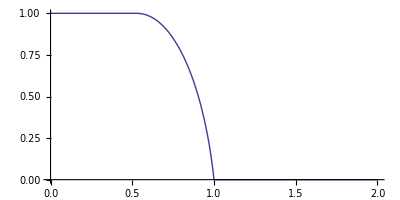

```mathematica
ParametricPlot[{pp2/pp1,Ng},{pp2,1,200000}]
```

```mathematica
qma
```

0.000928855 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-0.528282+pp2/100000])+0.682518 (-0.316228+√(0.1+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-0.528282+pp2/100000]))

```mathematica
T1
```

200

```mathematica
qmp2 =.
```

```mathematica
nmax=100;
qmlist=Array[a1,nmax];
qmdlist=Array[a2,{nmax,2}];
```

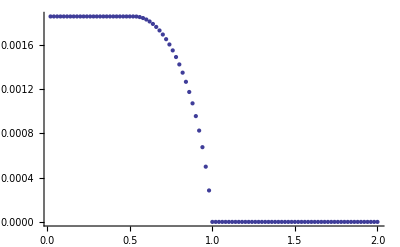

```mathematica
For[i=1,i<nmax+1,i++,
	pp2 = pp1 2 i/nmax;
	qmdlist[[i]]={pp2/pp1,AFa1[pp1,pp2]}
];
ListPlot[qmdlist]
```

```mathematica
eps =.;
kappa =.;
R = .;
cv = .;
Cd = .;
A0=.;
T1=.;
T2=.;
pp1=.;
pp2=.;
p10=.;
p20=.;
```

```mathematica
keps=.;
Kg=.;
Ndenom=.;
crit=.;
onPositive[x_]=.;
onNegative[x_]=.;
SqrabsL[x_,x0_]=.;
```

### Boundarys

```mathematica
boundaryEquations = { pp1 - (cp1 + Zcp1 dEp1 ),
           pp2 - (cp2 + Zcp2 dEp2 )};
```

### Expressions

The inlet flow is calculated as the outlet flow with reversed sign.

```mathematica
expressions = {{qmp1,-qmp2}};
```

Initial values

```mathematica
cp1/.Solve[boundaryEquations==0,{cp1,cp2}][[1]]
```

pp1-dEp1 Zcp1

```mathematica
initialExpressions={};
```

Calculation of parameters

```mathematica
localExpressions ={
		{kappa,1+R/cv,double,"polytrop coeff"},
		{keps,1/(-√eps+√(1+eps)),double,""},
		{Kg,√(kappa/R(2/(kappa+1))^((kappa+1)/(kappa-1))),double,""},
		{Ndenom,(kappa-1)/2(2/(kappa+1))^((kappa+1)/(kappa-1)),double,""},
		{crit,(2/(kappa+1))^(kappa/(kappa-1)),double,"Critical pressure drop"},
		{cp,cv+R,double,""}
	};
```

```mathematica
systemVariables
```

{qmp2,dEp1,dEp2,pp1,pp2}

```mathematica
Compgen[file]
```

Part::partw: Part 6 of PneumaticCport[1, 100000., "fluid port 1"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

XMLElement::cntsList: XMLElement["modelobject", « 1 », {XMLElement["icon", {"isopath" → "PneumaticOrifice.svg", "iconrotation" → "ON", "userpath" → "PneumaticOrifice.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.333333, "a" → "90", "name" → "P1"}, {}], XMLElement["portpose", {« 1 »}, {}], XMLElement["portpose", {"x" → 0.5, "y" → "0", "a" → "90", "name" → "PA0"}, {}]}]}] in XMLElement["hopsanobjectappearance", {"version" → "0.1"}, XMLElement["modelobject", {"typename" → "PneumaticOrifice", "displayname" → "PneumaticOrifice"}, {XMLElement["icon", {"isopath" → "PneumaticOrifice.svg", "iconrotation" → "ON", "userpath" → "PneumaticOrifice.svg"}, {}], XMLElement[« 1 »]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "y" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.666667 in "y" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.5 in "x" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

PneumaticOrifice.xml

## Q source

```mathematica
domain="Pneumatic";
displayName="Qsrc";
brief="Pneumatic massflow source";
componentType="ComponentQ";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFile[domain,displayName];
ResetComponentVariables[];
```

```mathematica
inputVariables  = {
{qminput,0.double,"kg/s","mass flow rate"},
{Tinput,273,double,"K","Temperature"}
			};
```

```mathematica
inputParameters = {
{cv,718,double,"","heatcoeff)"}
};
```

```mathematica
portConnections={
PneumaticQports[1,1.*10^5,"fluid port 1",{0,0.5,270}]
};
```

```mathematica
nodeConnections={
	PneumaticCport[1,100000.,"fluid port 1"]};
```

```mathematica
expressions = {
{qm1,qminput},
{dE1,(oPositive[qm1] qm1 cv Tin + onNegative[qm1] qm1 cv Tinput)},
{p1,cp1+ZcEP1 dE1}
};
```

```mathematica
Compgen[file]
```

Part::partw: Part 6 of PneumaticCport[1, 100000., "fluid port 1"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "" … "c", « 1 »}, {XMLElement["icon", {"isopath" → "PneumaticQsrc.svg", "iconrotation" → "ON", "userpath" → "PneumaticQsrc.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "P1"}, {}], XMLElement["portpose", {« 1 »}, {}], XMLElement["portpose", {"x" → 0.666667, "y" → "0", "a" → "90", "name" → "PTinput"}, {}]}]}] in « 1 » is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "x" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.666667 in "x" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

PneumaticQsrc.xml

## PT source

```mathematica
domain="Pneumatic";
displayName="PTsrc";
brief="Pneumatic pressure and temperature source";
componentType="ComponentC";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFile[domain,displayName];
ResetComponentVariables[];
```

```mathematica
inputVariables  = {
{pinput,1*10^5,double,"Pa","Input Pressure"},
{Tinput,273.,double,"K","Input Temperature"}
			};
```

```mathematica
nodeConnections={
PneumaticCports[1,1.*10^5,"fluid port 1",{0,0.5,270}]
};
```

```mathematica
nodeConnections={
	PneumaticCport[1,100000.,"fluid port 1",{0,0.5,270}]};
```

```mathematica
expressions = {
		{c1,pinput},
		{T1,Tinput},
		{Zc1, 0.}
			};
```

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {"t" … "me" → "" … "", « 1 »}, {XMLElement["icon", {"isopath" → "PneumaticPTsrc.svg", "iconrotation" → "ON", "userpath" → "PneumaticPTsrc.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.5, "a" → "90", "name" → "P1"}, {}], XMLElement["portpose", {« 1 »}, {}], XMLElement["portpose", {"x" → 0.666667, "y" → "0", "a" → "90", "name" → "PTinput"}, {}]}]}] in XMLElement[« 1 »] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.5 in "y" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "x" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.666667 in "x" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

PneumaticPTsrc.xml

```mathematica
portConnections
```

{PneumaticCports[1,100000.,fluid port 1,{0,0.5,270}]}